```mathematica
plotOptions=Sequence[BaseStyle->FontSize->18,FrameStyle->FontFamily->"Times",LabelStyle->GrayLevel[0],Frame->True,Axes->False,ImageSize->600,AspectRatio->0.8,GridLines->Automatic];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

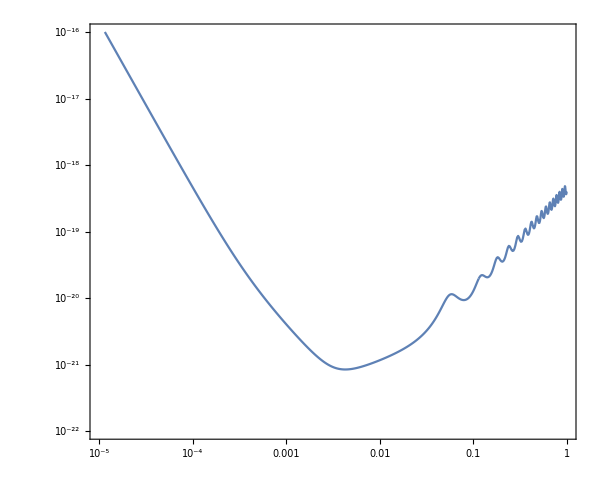

```mathematica
fsnData=ReadList["lisa_fsn.txt",{Number,Number}];

ListLogLogPlot[fsnData,Joined->True,Evaluate@plotOptions,PlotRange->{{10^-5,10^0},{10^-22,10^-16}}]
```